```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];Get["HopfE`"];
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[th3]:=Subscript[θ,3];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[bev]:=Subscript[β,v];
Format[v1]:=Subscript[v,1];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];Format[si]:=σ;Format[rh]:=ρ;
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
Format[c1]:=Subscript[c,1];Format[c2]:=Subscript[c,2];
(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)RN={0->"S","S"+"I1"->2*"I1","S"+"Y1"->"Y1"+"I1","I1"->"R1","S"+"I2"->2*"I2","S"+"Y2"->"Y2"+"I2","I2"->"R2","R1"+"I2"->"I2"+"Y2","R1"+"Y2"->2*"Y2","Y2"->"R","R2"+"I1"->"I1"+"Y1","R2"+"Y1"->2*"Y1","Y1"->"R","R1"->"S","R2"->"S","R"->"S","S"->0,"I1"->0,"Y1"->0,"R1"->0,"I2"->0,"Y2"->0,"R2"->0,"R"->0};
rts={mu,be1*I1*S,be1*et1*Y1*S,ga1*I1,be2*I2*S,be2*et2*Y2*S,ga2*I2,be2*si2*I2*R1,be2*si2*et2*Y2*R1,ga2*Y2,be1*si1*I1*R2,be1*si1*et1*Y1*R2,ga1*Y1,th1*R1,th2*R2,th3*R,mu*S,mu*I1,mu*Y1,mu*R1,mu*I2,mu*Y2,mu*R2,mu*R};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,R0A,EA,E1t,E2t} = bdAn[RN, rts];
Print["R1,R2 are",{R01,R02}=R0A/.E0," R21 is",R21=R0A[[2]]/.E1t[[2]]]
```

reactions and transitions: (0→S | μ
I1+S→2 I1 | β_1 I1 S
S+Y1→I1+Y1 | β_1 η_1 S Y1
I1→R1 | γ_1 I1
I2+S→2 I2 | β_2 I2 S
S+Y2→I2+Y2 | β_2 η_2 S Y2
I2→R2 | γ_2 I2
I2+R1→I2+Y2 | β_2 I2 R1 σ_2
R1+Y2→2 Y2 | β_2 η_2 R1 σ_2 Y2
Y2→R | γ_2 Y2
I1+R2→I1+Y1 | β_1 I1 R2 σ_1
R2+Y1→2 Y1 | β_1 η_1 R2 σ_1 Y1
Y1→R | γ_1 Y1
R1→S | R1 θ_1
R2→S | R2 θ_2
R→S | R θ_3
S→0 | μ S
I1→0 | I1 μ
Y1→0 | μ Y1
R1→0 | μ R1
I2→0 | I2 μ
Y2→0 | μ Y2
R2→0 | μ R2
R→0 | μ R)

RHS=(μ-β_1 I1 S-β_2 I2 S-μ S+R1 θ_1+R2 θ_2+R θ_3-β_1 η_1 S Y1-β_2 η_2 S Y2
-γ_1 I1-I1 μ+β_1 I1 S+β_1 η_1 S Y1
β_1 I1 R2 σ_1-γ_1 Y1-μ Y1+β_1 η_1 R2 σ_1 Y1
γ_1 I1-μ R1-β_2 I2 R1 σ_2-R1 θ_1-β_2 η_2 R1 σ_2 Y2
-γ_2 I2-I2 μ+β_2 I2 S+β_2 η_2 S Y2
β_2 I2 R1 σ_2-γ_2 Y2-μ Y2+β_2 η_2 R1 σ_2 Y2
γ_2 I2-μ R2-β_1 I1 R2 σ_1-R2 θ_2-β_1 η_1 R2 σ_1 Y1
-μ R-R θ_3+γ_1 Y1+γ_2 Y2) has var {S,I1,Y1,R1,I2,Y2,R2,R} par{β_1,β_2,η_1,η_2,γ_1,γ_2,μ,σ_1,σ_2,θ_1,θ_2,θ_3}

minimal siphons {{I1,Y1},{I2,Y2}} and invasion species are at positions: {2,3,5,6}

DFE solution E0: {R→0,R1→0,R2→0,S→1,I1→0,Y1→0,I2→0,Y2→0}

NGM K= ((β_1 S)/(γ_1+μ) | (β_1 η_1 S)/(γ_1+μ) | 0 | 0
(β_1 R2 σ_1)/(γ_1+μ) | (β_1 η_1 R2 σ_1)/(γ_1+μ) | 0 | 0
0 | 0 | (β_2 S)/(γ_2+μ) | (β_2 η_2 S)/(γ_2+μ)
0 | 0 | (β_2 R1 σ_2)/(γ_2+μ) | (β_2 η_2 R1 σ_2)/(γ_2+μ))

Eigenvalues: {0,0,(β_1 (S+η_1 R2 σ_1))/(γ_1+μ),(β_2 (S+η_2 R1 σ_2))/(γ_2+μ)}

Eigenvectors: {{0,0,-η_2,1},{-η_1,1,0,0},{S/(R2 σ_1),1,0,0},{0,0,S/(R1 σ_2),1}}

Nonzero eigenvalues: {(β_1 (S+η_1 R2 σ_1))/(γ_1+μ),(β_2 (S+η_2 R1 σ_2))/(γ_2+μ)}

Strain positions in NGM space - strain 1: {1,2}, strain 2: {3,4}

Processing eigenvalue 1 with eigenvector: {S/(R2 σ_1),1,0,0}

Strain 1 nonzero components = 2, Strain 2 nonzero components = 0

Processing eigenvalue 2 with eigenvector: {0,0,S/(R1 σ_2),1}

Strain 1 nonzero components = 0, Strain 2 nonzero components = 2

Strain associations: {1,2}

Ordered reproduction functions R0A: {(β_1 (S+η_1 R2 σ_1))/(γ_1+μ),(β_2 (S+η_2 R1 σ_2))/(γ_2+μ)}

R0A[[1]] (strain 1): (β_1 (S+η_1 R2 σ_1))/(γ_1+μ)

R0A[[2]] (strain 2): (β_2 (S+η_2 R1 σ_2))/(γ_2+μ)

Number of boundary systems= 2; first sys has 3 sols (3 rational), second sys has 3 sols (3 rational)

E1t rational solutions:

1: {I1→0,R→0,R1→0,R2→0,S→1,Y1→0}

2: {I1→((β_1-γ_1-μ) (μ+θ_1))/(β_1 (γ_1+μ+θ_1)),R→0,R1→(γ_1 (β_1-γ_1-μ))/(β_1 (γ_1+μ+θ_1)),R2→0,S→(γ_1+μ)/β_1,Y1→0}

3: {I1→-(((μ+θ_1) (μ+θ_2) (β_1 η_1 μ σ_1+γ_1 θ_2+μ θ_2-γ_1 θ_3+β_1 η_1 σ_1 θ_3+θ_2 θ_3))/(β_1 σ_1 (-η_1 γ_1 μ^2-η_1 μ^3+η_1 γ_1 μ^2 σ_1+η_1 μ^3 σ_1-η_1 μ^2 θ_1+η_1 γ_1 μ σ_1 θ_1+η_1 μ^2 σ_1 θ_1+γ_1 μ θ_2-η_1 γ_1 μ θ_2+μ^2 θ_2-η_1 μ^2 θ_2+γ_1 θ_1 θ_2+μ θ_1 θ_2-η_1 μ θ_1 θ_2-γ_1 μ θ_3-η_1 γ_1 μ θ_3-η_1 μ^2 θ_3+η_1 γ_1 μ σ_1 θ_3+η_1 μ^2 σ_1 θ_3-γ_1 θ_1 θ_3-η_1 μ θ_1 θ_3+η_1 γ_1 σ_1 θ_1 θ_3+η_1 μ σ_1 θ_1 θ_3-η_1 γ_1 θ_2 θ_3+μ θ_2 θ_3-η_1 μ θ_2 θ_3+θ_1 θ_2 θ_3-η_1 θ_1 θ_2 θ_3))),R→(γ_1 (μ+θ_2) (γ_1 μ+μ^2+β_1 μ σ_1-γ_1 μ σ_1-μ^2 σ_1+μ θ_1+β_1 σ_1 θ_1-γ_1 σ_1 θ_1-μ σ_1 θ_1+γ_1 θ_2+μ θ_2+θ_1 θ_2))/(β_1 σ_1 (-η_1 γ_1 μ^2-η_1 μ^3+η_1 γ_1 μ^2 σ_1+η_1 μ^3 σ_1-η_1 μ^2 θ_1+η_1 γ_1 μ σ_1 θ_1+η_1 μ^2 σ_1 θ_1+γ_1 μ θ_2-η_1 γ_1 μ θ_2+μ^2 θ_2-η_1 μ^2 θ_2+γ_1 θ_1 θ_2+μ θ_1 θ_2-η_1 μ θ_1 θ_2-γ_1 μ θ_3-η_1 γ_1 μ θ_3-η_1 μ^2 θ_3+η_1 γ_1 μ σ_1 θ_3+η_1 μ^2 σ_1 θ_3-γ_1 θ_1 θ_3-η_1 μ θ_1 θ_3+η_1 γ_1 σ_1 θ_1 θ_3+η_1 μ σ_1 θ_1 θ_3-η_1 γ_1 θ_2 θ_3+μ θ_2 θ_3-η_1 μ θ_2 θ_3+θ_1 θ_2 θ_3-η_1 θ_1 θ_2 θ_3)),R1→-((γ_1 (μ+θ_2) (β_1 η_1 μ σ_1+γ_1 θ_2+μ θ_2-γ_1 θ_3+β_1 η_1 σ_1 θ_3+θ_2 θ_3))/(β_1 σ_1 (-η_1 γ_1 μ^2-η_1 μ^3+η_1 γ_1 μ^2 σ_1+η_1 μ^3 σ_1-η_1 μ^2 θ_1+η_1 γ_1 μ σ_1 θ_1+η_1 μ^2 σ_1 θ_1+γ_1 μ θ_2-η_1 γ_1 μ θ_2+μ^2 θ_2-η_1 μ^2 θ_2+γ_1 θ_1 θ_2+μ θ_1 θ_2-η_1 μ θ_1 θ_2-γ_1 μ θ_3-η_1 γ_1 μ θ_3-η_1 μ^2 θ_3+η_1 γ_1 μ σ_1 θ_3+η_1 μ^2 σ_1 θ_3-γ_1 θ_1 θ_3-η_1 μ θ_1 θ_3+η_1 γ_1 σ_1 θ_1 θ_3+η_1 μ σ_1 θ_1 θ_3-η_1 γ_1 θ_2 θ_3+μ θ_2 θ_3-η_1 μ θ_2 θ_3+θ_1 θ_2 θ_3-η_1 θ_1 θ_2 θ_3))),R2→-(((γ_1+μ) (γ_1 μ+μ^2+β_1 μ σ_1-γ_1 μ σ_1-μ^2 σ_1+μ θ_1+β_1 σ_1 θ_1-γ_1 σ_1 θ_1-μ σ_1 θ_1+γ_1 θ_2+μ θ_2+θ_1 θ_2) (μ+θ_3))/(β_1 σ_1 (-η_1 γ_1 μ^2-η_1 μ^3+η_1 γ_1 μ^2 σ_1+η_1 μ^3 σ_1-η_1 μ^2 θ_1+η_1 γ_1 μ σ_1 θ_1+η_1 μ^2 σ_1 θ_1+γ_1 μ θ_2-η_1 γ_1 μ θ_2+μ^2 θ_2-η_1 μ^2 θ_2+γ_1 θ_1 θ_2+μ θ_1 θ_2-η_1 μ θ_1 θ_2-γ_1 μ θ_3-η_1 γ_1 μ θ_3-η_1 μ^2 θ_3+η_1 γ_1 μ σ_1 θ_3+η_1 μ^2 σ_1 θ_3-γ_1 θ_1 θ_3-η_1 μ θ_1 θ_3+η_1 γ_1 σ_1 θ_1 θ_3+η_1 μ σ_1 θ_1 θ_3-η_1 γ_1 θ_2 θ_3+μ θ_2 θ_3-η_1 μ θ_2 θ_3+θ_1 θ_2 θ_3-η_1 θ_1 θ_2 θ_3))),S→((γ_1+μ) (μ+θ_1) (β_1 η_1 μ σ_1+γ_1 θ_2+μ θ_2-γ_1 θ_3+β_1 η_1 σ_1 θ_3+θ_2 θ_3))/(β_1 (-η_1 γ_1 μ^2-η_1 μ^3+η_1 γ_1 μ^2 σ_1+η_1 μ^3 σ_1-η_1 μ^2 θ_1+η_1 γ_1 μ σ_1 θ_1+η_1 μ^2 σ_1 θ_1+γ_1 μ θ_2-η_1 γ_1 μ θ_2+μ^2 θ_2-η_1 μ^2 θ_2+γ_1 θ_1 θ_2+μ θ_1 θ_2-η_1 μ θ_1 θ_2-γ_1 μ θ_3-η_1 γ_1 μ θ_3-η_1 μ^2 θ_3+η_1 γ_1 μ σ_1 θ_3+η_1 μ^2 σ_1 θ_3-γ_1 θ_1 θ_3-η_1 μ θ_1 θ_3+η_1 γ_1 σ_1 θ_1 θ_3+η_1 μ σ_1 θ_1 θ_3-η_1 γ_1 θ_2 θ_3+μ θ_2 θ_3-η_1 μ θ_2 θ_3+θ_1 θ_2 θ_3-η_1 θ_1 θ_2 θ_3)),Y1→((μ+θ_2) (γ_1 μ+μ^2+β_1 μ σ_1-γ_1 μ σ_1-μ^2 σ_1+μ θ_1+β_1 σ_1 θ_1-γ_1 σ_1 θ_1-μ σ_1 θ_1+γ_1 θ_2+μ θ_2+θ_1 θ_2) (μ+θ_3))/(β_1 σ_1 (-η_1 γ_1 μ^2-η_1 μ^3+η_1 γ_1 μ^2 σ_1+η_1 μ^3 σ_1-η_1 μ^2 θ_1+η_1 γ_1 μ σ_1 θ_1+η_1 μ^2 σ_1 θ_1+γ_1 μ θ_2-η_1 γ_1 μ θ_2+μ^2 θ_2-η_1 μ^2 θ_2+γ_1 θ_1 θ_2+μ θ_1 θ_2-η_1 μ θ_1 θ_2-γ_1 μ θ_3-η_1 γ_1 μ θ_3-η_1 μ^2 θ_3+η_1 γ_1 μ σ_1 θ_3+η_1 μ^2 σ_1 θ_3-γ_1 θ_1 θ_3-η_1 μ θ_1 θ_3+η_1 γ_1 σ_1 θ_1 θ_3+η_1 μ σ_1 θ_1 θ_3-η_1 γ_1 θ_2 θ_3+μ θ_2 θ_3-η_1 μ θ_2 θ_3+θ_1 θ_2 θ_3-η_1 θ_1 θ_2 θ_3))}

E2t rational solutions:

1: {I2→0,R→0,R1→0,R2→0,S→1,Y2→0}

2: {I2→((β_2-γ_2-μ) (μ+θ_2))/(β_2 (γ_2+μ+θ_2)),R→0,R1→0,R2→(γ_2 (β_2-γ_2-μ))/(β_2 (γ_2+μ+θ_2)),S→(γ_2+μ)/β_2,Y2→0}

3: {I2→-(((μ+θ_1) (μ+θ_2) (β_2 η_2 μ σ_2+γ_2 θ_1+μ θ_1-γ_2 θ_3+β_2 η_2 σ_2 θ_3+θ_1 θ_3))/(β_2 σ_2 (-η_2 γ_2 μ^2-η_2 μ^3+η_2 γ_2 μ^2 σ_2+η_2 μ^3 σ_2+γ_2 μ θ_1-η_2 γ_2 μ θ_1+μ^2 θ_1-η_2 μ^2 θ_1-η_2 μ^2 θ_2+η_2 γ_2 μ σ_2 θ_2+η_2 μ^2 σ_2 θ_2+γ_2 θ_1 θ_2+μ θ_1 θ_2-η_2 μ θ_1 θ_2-γ_2 μ θ_3-η_2 γ_2 μ θ_3-η_2 μ^2 θ_3+η_2 γ_2 μ σ_2 θ_3+η_2 μ^2 σ_2 θ_3-η_2 γ_2 θ_1 θ_3+μ θ_1 θ_3-η_2 μ θ_1 θ_3-γ_2 θ_2 θ_3-η_2 μ θ_2 θ_3+η_2 γ_2 σ_2 θ_2 θ_3+η_2 μ σ_2 θ_2 θ_3+θ_1 θ_2 θ_3-η_2 θ_1 θ_2 θ_3))),R→(γ_2 (μ+θ_1) (γ_2 μ+μ^2+β_2 μ σ_2-γ_2 μ σ_2-μ^2 σ_2+γ_2 θ_1+μ θ_1+μ θ_2+β_2 σ_2 θ_2-γ_2 σ_2 θ_2-μ σ_2 θ_2+θ_1 θ_2))/(β_2 σ_2 (-η_2 γ_2 μ^2-η_2 μ^3+η_2 γ_2 μ^2 σ_2+η_2 μ^3 σ_2+γ_2 μ θ_1-η_2 γ_2 μ θ_1+μ^2 θ_1-η_2 μ^2 θ_1-η_2 μ^2 θ_2+η_2 γ_2 μ σ_2 θ_2+η_2 μ^2 σ_2 θ_2+γ_2 θ_1 θ_2+μ θ_1 θ_2-η_2 μ θ_1 θ_2-γ_2 μ θ_3-η_2 γ_2 μ θ_3-η_2 μ^2 θ_3+η_2 γ_2 μ σ_2 θ_3+η_2 μ^2 σ_2 θ_3-η_2 γ_2 θ_1 θ_3+μ θ_1 θ_3-η_2 μ θ_1 θ_3-γ_2 θ_2 θ_3-η_2 μ θ_2 θ_3+η_2 γ_2 σ_2 θ_2 θ_3+η_2 μ σ_2 θ_2 θ_3+θ_1 θ_2 θ_3-η_2 θ_1 θ_2 θ_3)),R1→-(((γ_2+μ) (γ_2 μ+μ^2+β_2 μ σ_2-γ_2 μ σ_2-μ^2 σ_2+γ_2 θ_1+μ θ_1+μ θ_2+β_2 σ_2 θ_2-γ_2 σ_2 θ_2-μ σ_2 θ_2+θ_1 θ_2) (μ+θ_3))/(β_2 σ_2 (-η_2 γ_2 μ^2-η_2 μ^3+η_2 γ_2 μ^2 σ_2+η_2 μ^3 σ_2+γ_2 μ θ_1-η_2 γ_2 μ θ_1+μ^2 θ_1-η_2 μ^2 θ_1-η_2 μ^2 θ_2+η_2 γ_2 μ σ_2 θ_2+η_2 μ^2 σ_2 θ_2+γ_2 θ_1 θ_2+μ θ_1 θ_2-η_2 μ θ_1 θ_2-γ_2 μ θ_3-η_2 γ_2 μ θ_3-η_2 μ^2 θ_3+η_2 γ_2 μ σ_2 θ_3+η_2 μ^2 σ_2 θ_3-η_2 γ_2 θ_1 θ_3+μ θ_1 θ_3-η_2 μ θ_1 θ_3-γ_2 θ_2 θ_3-η_2 μ θ_2 θ_3+η_2 γ_2 σ_2 θ_2 θ_3+η_2 μ σ_2 θ_2 θ_3+θ_1 θ_2 θ_3-η_2 θ_1 θ_2 θ_3))),R2→-((γ_2 (μ+θ_1) (β_2 η_2 μ σ_2+γ_2 θ_1+μ θ_1-γ_2 θ_3+β_2 η_2 σ_2 θ_3+θ_1 θ_3))/(β_2 σ_2 (-η_2 γ_2 μ^2-η_2 μ^3+η_2 γ_2 μ^2 σ_2+η_2 μ^3 σ_2+γ_2 μ θ_1-η_2 γ_2 μ θ_1+μ^2 θ_1-η_2 μ^2 θ_1-η_2 μ^2 θ_2+η_2 γ_2 μ σ_2 θ_2+η_2 μ^2 σ_2 θ_2+γ_2 θ_1 θ_2+μ θ_1 θ_2-η_2 μ θ_1 θ_2-γ_2 μ θ_3-η_2 γ_2 μ θ_3-η_2 μ^2 θ_3+η_2 γ_2 μ σ_2 θ_3+η_2 μ^2 σ_2 θ_3-η_2 γ_2 θ_1 θ_3+μ θ_1 θ_3-η_2 μ θ_1 θ_3-γ_2 θ_2 θ_3-η_2 μ θ_2 θ_3+η_2 γ_2 σ_2 θ_2 θ_3+η_2 μ σ_2 θ_2 θ_3+θ_1 θ_2 θ_3-η_2 θ_1 θ_2 θ_3))),S→((γ_2+μ) (μ+θ_2) (β_2 η_2 μ σ_2+γ_2 θ_1+μ θ_1-γ_2 θ_3+β_2 η_2 σ_2 θ_3+θ_1 θ_3))/(β_2 (-η_2 γ_2 μ^2-η_2 μ^3+η_2 γ_2 μ^2 σ_2+η_2 μ^3 σ_2+γ_2 μ θ_1-η_2 γ_2 μ θ_1+μ^2 θ_1-η_2 μ^2 θ_1-η_2 μ^2 θ_2+η_2 γ_2 μ σ_2 θ_2+η_2 μ^2 σ_2 θ_2+γ_2 θ_1 θ_2+μ θ_1 θ_2-η_2 μ θ_1 θ_2-γ_2 μ θ_3-η_2 γ_2 μ θ_3-η_2 μ^2 θ_3+η_2 γ_2 μ σ_2 θ_3+η_2 μ^2 σ_2 θ_3-η_2 γ_2 θ_1 θ_3+μ θ_1 θ_3-η_2 μ θ_1 θ_3-γ_2 θ_2 θ_3-η_2 μ θ_2 θ_3+η_2 γ_2 σ_2 θ_2 θ_3+η_2 μ σ_2 θ_2 θ_3+θ_1 θ_2 θ_3-η_2 θ_1 θ_2 θ_3)),Y2→((μ+θ_1) (γ_2 μ+μ^2+β_2 μ σ_2-γ_2 μ σ_2-μ^2 σ_2+γ_2 θ_1+μ θ_1+μ θ_2+β_2 σ_2 θ_2-γ_2 σ_2 θ_2-μ σ_2 θ_2+θ_1 θ_2) (μ+θ_3))/(β_2 σ_2 (-η_2 γ_2 μ^2-η_2 μ^3+η_2 γ_2 μ^2 σ_2+η_2 μ^3 σ_2+γ_2 μ θ_1-η_2 γ_2 μ θ_1+μ^2 θ_1-η_2 μ^2 θ_1-η_2 μ^2 θ_2+η_2 γ_2 μ σ_2 θ_2+η_2 μ^2 σ_2 θ_2+γ_2 θ_1 θ_2+μ θ_1 θ_2-η_2 μ θ_1 θ_2-γ_2 μ θ_3-η_2 γ_2 μ θ_3-η_2 μ^2 θ_3+η_2 γ_2 μ σ_2 θ_3+η_2 μ^2 σ_2 θ_3-η_2 γ_2 θ_1 θ_3+μ θ_1 θ_3-η_2 μ θ_1 θ_3-γ_2 θ_2 θ_3-η_2 μ θ_2 θ_3+η_2 γ_2 σ_2 θ_2 θ_3+η_2 μ σ_2 θ_2 θ_3+θ_1 θ_2 θ_3-η_2 θ_1 θ_2 θ_3))}

R1,R2 are{β_1/(γ_1+μ),β_2/(γ_2+μ)} R21 is(β_2 ((γ_1+μ)/β_1+(η_2 γ_1 (β_1-γ_1-μ) σ_2)/(β_1 (γ_1+μ+θ_1))))/(γ_2+μ)

```mathematica
{E1,E2,R12,R21,coP}=invNr[E1t,E2t,R0A,E0,par,cp,2,2];
coP
```

Selected E1 (solution 2): {I1→((β_1-γ_1-μ) (μ+θ_1))/(β_1 (γ_1+μ+θ_1)),R→0,R1→(γ_1 (β_1-γ_1-μ))/(β_1 (γ_1+μ+θ_1)),R2→0,S→(γ_1+μ)/β_1,Y1→0}

Selected E2 (solution 2): {I2→((β_2-γ_2-μ) (μ+θ_2))/(β_2 (γ_2+μ+θ_2)),R→0,R1→0,R2→(γ_2 (β_2-γ_2-μ))/(β_2 (γ_2+μ+θ_2)),S→(γ_2+μ)/β_2,Y2→0}

invasion numbers are{(β_2 (γ_1^2+2 γ_1 μ+μ^2+β_1 η_2 γ_1 σ_2-η_2 γ_1^2 σ_2-η_2 γ_1 μ σ_2+γ_1 θ_1+μ θ_1))/(β_1 (γ_2+μ) (γ_1+μ+θ_1)),(β_1 (γ_2^2+2 γ_2 μ+μ^2+β_2 η_1 γ_2 σ_1-η_1 γ_2^2 σ_1-η_1 γ_2 μ σ_1+γ_2 θ_2+μ θ_2))/(β_2 (γ_1+μ) (γ_2+μ+θ_2))}

under coP: {β_1→4,β_2→3,η_1→1,η_2→1,γ_1→1,γ_2→1,μ→1,σ_1→1,σ_2→1,θ_1→1/2,θ_2→1,θ_3→1} invasion nrs are{1.05,1.55556} repr nrs are{2.,1.5}

END invNr OUTPUT

{β_1→4,β_2→3,η_1→1,η_2→1,γ_1→1,γ_2→1,μ→1,σ_1→1,σ_2→1,θ_1→1/2,θ_2→1,θ_3→1}

Auto-determined varInd: {1,2,5}

Susceptible: S

Strain 1 (first compartment): I1

Strain 2 (first compartment): I2

Checked 730 potential coexistence points

All Rij equations: {β_1/2==1,β_2/2==1,((3+β_1) β_2)/(5 β_1)==1,(β_1 (4+β_2))/(6 β_2)==1}

DFE: 221 (9%)

E2: 612 (24%)

E1: 937 (37%)

EE-Unstable: 730 (29%)

{18.6563,Null}

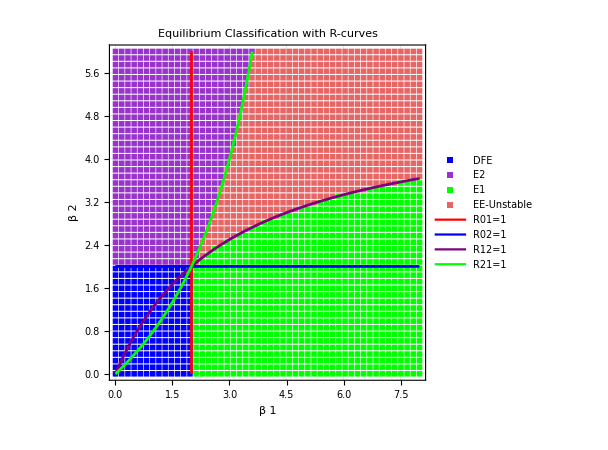

```mathematica
{R01,R02}=R0A/.E0;gridRes=50;plotInd={1,2};steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[(*Step 3:Scanning-now with mSi from step 1*)
{plot,noSol,results}=scan[RHS,var,par,coP,plotInd,mSi,(*mSi auto-provided*)gridRes,steadyTol,stabTol,chopTol,R01,R02,R12,R21];]
plot
```

```mathematica
Export["GavScan.pdf",fPl]
```

GavScan.pdf